Data Import

```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210421_OR_model_and_other_lines_sliding"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
datafull=Import["../data/pltcm_manipulated_64026.csv"];
```

Data with Sliding Time Windows

```mathematica
x1=Round@Ceiling[Length@datafull/8,1];
{a,b,c,d,e,f,g,h}=Join[Range[x1,Length@datafull,x1],{Length@datafull}];
data1=Join[{Take[datafull,{1,a}]},Flatten[Table[{Take[datafull,{z[[1]]-x1/2,z[[2]]-x1/2}],Take[datafull,{z[[1]],z[[2]]}]},{z,
Partition[{a,b,c,d,e,f,g,h},2,1]}],1]];
win1=Length@data1;
```

```mathematica
x2=Round@Ceiling[Length@datafull/16,1];
{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p}=Join[Range[x2,Length@datafull,x2],{Length@datafull}];
data2=Join[{Take[datafull,{1,a}]},Flatten[Table[{Take[datafull,{z[[1]]-x2/2,z[[2]]-x2/2}],Take[datafull,{z[[1]],z[[2]]}]},{z,
Partition[{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p},2,1]}],1]];
win2=Length@data2;
```

```mathematica
<<IGraphM`
```

IGraph/M 0.5.1 (October 12, 2020)
Evaluate IGDocumentation[] to get started.

Fixed Step Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep1=snetworkdatabinnedintimewindows[data1,9,11,win1];]
```

{11.8704,Null}

```mathematica
graphsandnodenumbers1=Table[snetworkgraph[widthdataintimewindowsFixedstep1[[1]][[i]],widthdataintimewindowsFixedstep1[[2]][[i]],2,7,400,Green],{i,Range@win1}];
```

```mathematica
modularityvalue=N@GraphAssortativity[graphsandnodenumbers1[[1,1]],FindGraphCommunities[graphsandnodenumbers1[[1,1]]],"Normalized"->False]
```

0.0793102

```mathematica
randomnesselements[network_]:=
Module[{X,randomgraphserdösrenyi,modularityerdösrenyi,μerdösrenyi,σerdösrenyi,
randomgraphsdegreesfxd,modularitydegreesfxd,μdegreesfxd,σdegreesfxd,randomgraphscomm,
modularitycomm,μcomm,σcomm,ZScores},

X=N@GraphAssortativity[network,FindGraphCommunities[network],"Normalized"->False];

randomgraphserdösrenyi=RandomGraph[{VertexCount[network],EdgeCount[network]},1000];
modularityerdösrenyi=Table[N@GraphAssortativity[
randomgraphserdösrenyi[[i]],FindGraphCommunities[randomgraphserdösrenyi[[i]]],
"Normalized"->False],{i,1000}];
μerdösrenyi=Mean[Table[modularityerdösrenyi[[i]],{i,1000}]];
σerdösrenyi=StandardDeviation[Table[modularityerdösrenyi[[i]],{i,1000}]];

randomgraphsdegreesfxd=Table[Symbol["IGDegreeSequenceGame"][Total[AdjacencyMatrix@network],
Method->"VigerLatapy"],{i,1000}];
modularitydegreesfxd=Table[N@GraphAssortativity[
randomgraphsdegreesfxd[[i]],FindGraphCommunities[randomgraphsdegreesfxd[[i]]],
"Normalized"->False],{i,1000}];
μdegreesfxd=Mean[Table[modularitydegreesfxd[[i]],{i,1000}]];
σdegreesfxd=StandardDeviation[Table[modularitydegreesfxd[[i]],{i,1000}]];

randomgraphscomm=Table[randomizedgraphamongcommunities[network],1000];
modularitycomm=Table[N@GraphAssortativity[
randomgraphscomm[[i]],FindGraphCommunities[randomgraphscomm[[i]]],"Normalized"->False],
{i,1000}];
μcomm=Mean[Table[modularitycomm[[i]],{i,1000}]];
σcomm=StandardDeviation[Table[modularitycomm[[i]],{i,1000}]];

ZScores={(X-μerdösrenyi)/σerdösrenyi,(X-μdegreesfxd)/σdegreesfxd,(X-μcomm)/σcomm};
{{modularityerdösrenyi,modularitydegreesfxd,modularitycomm},ZScores}]
```

```mathematica
AbsoluteTiming[trial=randomnesselements[graphsandnodenumbers1[[1,1]]];]
```

{59.3277,Null}

```mathematica
trial[[2]]
```

{5.23405,9.56934,-88.6454}

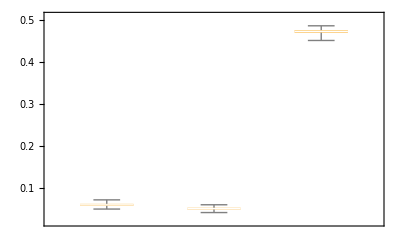

```mathematica
plot=BoxWhiskerChart[trial[[1,{1,2,3}]]]
```

```mathematica
compressYAxis[%59,{0.04,0.08},{0.44,0.49}]
```

-Graphics-

```mathematica
Clear[compressYAxis];
compressYAxis[plot_,range1_,range2_]:=Module[{ytick1,ytick2,epilog1,target},ytick1=FindDivisions[range1,5]/. y_?NumericQ:>{y,y}/. {y_?NumericQ,_}/;y≥range1[[2]]:>Sequence[];
ytick2=FindDivisions[range2,5]/. y_?NumericQ:>{y-range2[[1]]+range1[[2]],y}/. {y_?NumericQ,_}/;y≤range1[[2]]:>Sequence[];
epilog=Options[plot,Epilog][[1,2]];
target=Subtract@@Reverse@range1/(Subtract@@Reverse@range1+Subtract@@Reverse@range2);
Show[plot/. {x_?NumericQ,y_?NumericQ/;y>range2[[1]]}:>{x,y-range2[[1]]+range1[[2]]},PlotRange->{range1[[1]],range1[[2]]+Subtract@@Reverse@range2},Ticks->{Automatic,Join[ytick1,ytick2]},Epilog->Join[epilog,{White,Rectangle[Scaled[{-0.1,0.98 target}],Scaled[{1.1,1.02 target}]],Black,Text[Rotate["\\",π/2],Scaled[{0,0.98 target}],{-1.5,0}],Text[Rotate["\\",π/2],Scaled[{0,1.02 target}],{-1.5,0}]}]]]
```

```mathematica
data1={{1,1.1},{2,1.5},{3,0.9},{4,2.3},{5,1.1}};
data2={{1,1001.1},{2,1001.5},{3,1000.9},{4,1002.3},{5,1001.1}};

p=ListLinePlot[{data1,data2},PlotRange->All,PlotLabel->"Example of a compressed y axis",AxesLabel->{"x","y"}];

compressYAxis[p,{0,3},{999,1003}]
```

-Graphics-

```mathematica
data1={{1,1.1},{2,1.5},{3,0.9},{4,2.3},{5,1.1}};
data2={{1,1001.1},{2,1001.5},{3,1000.9},{4,1002.3},{5,1001.1}};
```

```mathematica
plot=ListLinePlot[{data1,data2},PlotRange->All,PlotLabel->"Example of a compressed y axis",AxesLabel->{"x","y"}];
range1={0,3};
range2={999,1003};
ytick1=FindDivisions[range1,5]/. y_?NumericQ:>{y,y}/. {y_?NumericQ,_}/;y≥range1[[2]]:>Sequence[]
ytick2=FindDivisions[range2,5]/. y_?NumericQ:>{y-range2[[1]]+range1[[2]],y}/. {y_?NumericQ,_}/;y≤range1[[2]]:>Sequence[]
```

{{0,0},{1,1},{2,2}}

{{4,1000},{5,1001},{6,1002},{7,1003}}

```mathematica
plot=BoxWhiskerChart[trial[[1,{1,2,3}]]];
range1={0,0.1};
range2={0.4,0.5};
ytick1=N@FindDivisions[range1,5]/. y_?NumericQ:>{y,y}/. {y_?NumericQ,_}/;y≥range1[[2]]:>Sequence[]
ytick2=N@FindDivisions[range2,5]/. y_?NumericQ:>{y-range2[[1]]+range1[[2]],y}/. {y_?NumericQ,_}/;y≤range1[[2]]:>Sequence[]
```

{{0.,0.},{0.02,0.02},{0.04,0.04},{0.06,0.06},{0.08,0.08}}

{{0.12,0.42},{0.14,0.44},{0.16,0.46},{0.18,0.48},{0.2,0.5}}

```mathematica
epilog=Options[plot,Epilog][[1,2]]
```

```mathematica
target=Subtract@@Reverse@range1/(Subtract@@Reverse@range1+Subtract@@Reverse@range2);
```

```mathematica
Show[plot/. {x_?NumericQ,y_?NumericQ/;y>range2[[1]]}:>{x,y-range2[[1]]+range1[[2]]},PlotRange->{range1[[1]],range1[[2]]+Subtract@@Reverse@range2},Ticks->{Automatic,Join[ytick1,ytick2]},Epilog->{White,Rectangle[Scaled[{-0.1,0.98 target}],Scaled[{1.1,1.02 target}]],Black,Text[Rotate["\\",π/2],Scaled[{0,0.98 target}],{-1.5,0}],Text[Rotate["\\",π/2],Scaled[{0,1.02 target}],{-1.5,0}]}]
```

-Graphics-